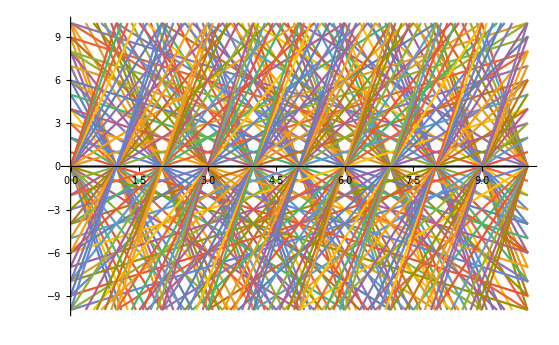

```mathematica
Clear["Global`*"];
flin[t_, a_, c_]:=Module[{x=0},x=a*(t-c);x];
(* plot the space of linear functions *)
Plot[Evaluate@Table[flin[t,a,c],{a,-10,10,1},{c,0,10,1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}]
```

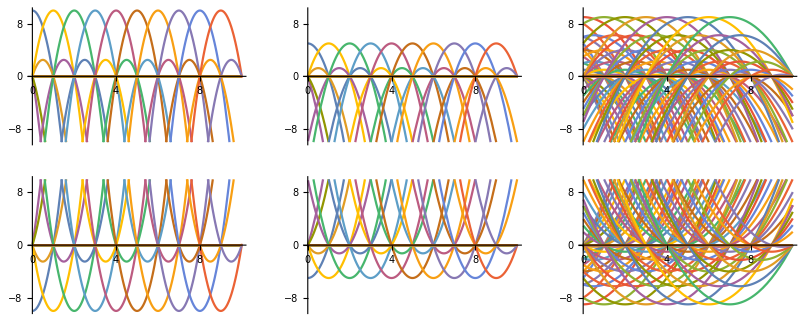

```mathematica
fquad[t_, a_, b_, c_]:=Module[{x=0,r=0},
x=c*(t-a)*(t-b);
If[b>a-1,x=0];
If[b≠a,r=Abs[(b-a)*(a-b)/4],r=1];
If[Abs[c]>10/r,x=0];
x];
(* plot the space of quadratic functions *)
(*Plot[fquad[t,8,6,-10],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] *)
p1=Plot[Evaluate@Table[fquad[t,a,b,-10],{a,0,10,1},{b,-10,10,1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p2=Plot[Evaluate@Table[fquad[t,a,b,-5],{a,0,10,1},{b,-10,10,1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p3=Plot[Evaluate@Table[fquad[t,a,b,-1],{a,0,10,1},{b,-10,10,1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p4=Plot[Evaluate@Table[fquad[t,a,b,+10],{a,0,10,1},{b,-10,10,1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p5=Plot[Evaluate@Table[fquad[t,a,b,+5],{a,0,10,1},{b,-10,10,1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p6=Plot[Evaluate@Table[fquad[t,a,b,+1],{a,0,10,1},{b,-10,10,1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
GraphicsGrid[{{p1,p2,p3},{p4,p5,p6}}]
```

```mathematica
Roots[(t-b)*(t-c)+(t-a)*(t-c)+(t-a)*(t-b)==0,t]
```

t==1/3 (a+b+c-√(a^2-a b+b^2-a c-b c+c^2))||t==1/3 (a+b+c+√(a^2-a b+b^2-a c-b c+c^2))

```mathematica
fcubic[t_, a_, b_, c_,d_]:=Module[{x=0,r1=0,r2=0,v1=0,v2=0},
x=d*(t-a)*(t-b)*(t-c);
If[b>a-1,x=0];
If[c>b -1 || c>a-1, x=0];
r1=(a+b+c-Sqrt[a*a-a*b+b*b-a*c-b*c+c*c])/3;
r2=(a+b+c+Sqrt[a*a-a*b+b*b-a*c-b*c+c*c])/3;
v1=d*(r1-a)*(r1-b)*(r1-c);
v2=d*(r2-a)*(r2-b)*(r2-c);
If[Abs[v1]>10 || Abs[v2]>10,x=0];
x];
(* plot the space of cubic functions *)
(* Plot[fcubic[t,8,5,-2,0.08],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] *)
p1=Plot[Evaluate@Table[fcubic[t,a,b,-5,0.01],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];
p2=Plot[Evaluate@Table[fcubic[t,a,b,-5,0.05],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];
p3=Plot[Evaluate@Table[fcubic[t,a,b,-5,0.10],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];

p4=Plot[Evaluate@Table[fcubic[t,a,b,-1,0.05],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];
p5=Plot[Evaluate@Table[fcubic[t,a,b,-1,0.08],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];
p6=Plot[Evaluate@Table[fcubic[t,a,b,-1,0.10],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];

p7=Plot[Evaluate@Table[fcubic[t,a,b,+3,0.1],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];
p8=Plot[Evaluate@Table[fcubic[t,a,b,+3,0.2],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];
p9=Plot[Evaluate@Table[fcubic[t,a,b,+3,0.3],{a,0,10,1},{b,-10,10,2}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}} ];

GraphicsGrid[{{p1,p2,p3},{p4,p5,p6}, {p7,p8,p9}}]
```

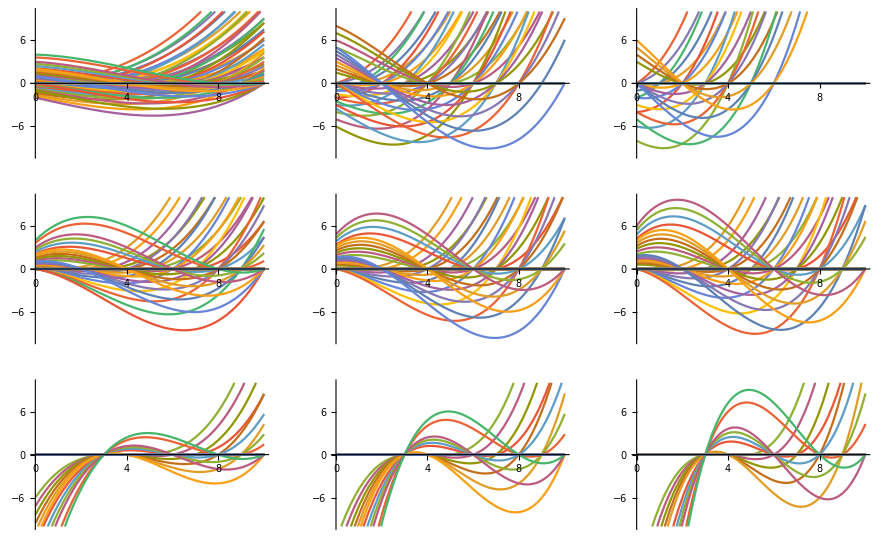

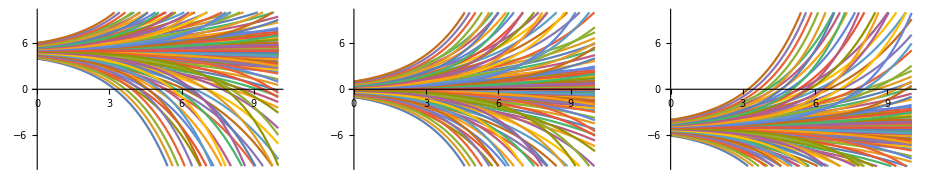

```mathematica
fexp[t_, a_, b_, c_]:=Module[{x=0,r=0},
x=b*Exp[a*t]+c;
x];
p1=Plot[Evaluate@Table[fexp[t,a,b,5],{a,-0.5,0.5,0.1},{b,-1,1,0.1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p2=Plot[Evaluate@Table[fexp[t,a,b,0],{a,-0.5,0.5,0.1},{b,-1,1,0.1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p3=Plot[Evaluate@Table[fexp[t,a,b,-5],{a,-0.5,0.5,0.1},{b,-1,1,0.1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;

GraphicsGrid[{{p1,p2,p3}}]
```

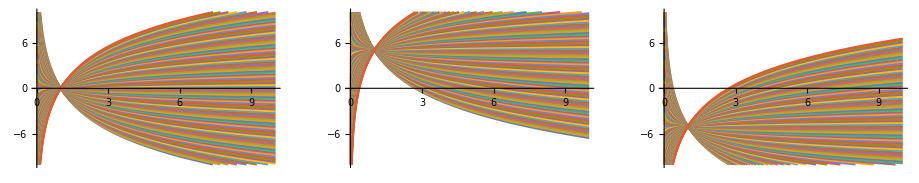

```mathematica
flog[t_, a_, b_]:=Module[{x=0,r=0},
x=a*Log[t]+b;
x];
p1=Plot[Evaluate@Table[flog[t,a,0],{a,-5.0,5.0,0.1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p2=Plot[Evaluate@Table[flog[t,a,5],{a,-5.0,5.0,0.1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
p3=Plot[Evaluate@Table[flog[t,a,-5],{a,-5.0,5.0,0.1}],{t,0.01,10.01}, PlotRange->{{0,10},{-10,10}}] ;
GraphicsGrid[{{p1,p2,p3}}]
```